# Nihanje nosilca

## Direktna metoda

Enačbo w_xxxx+w_tt=q, ki opisuje nihanje nosilca, rešujemo z metodo delne itegracije. Odvode po x aproksimiramo z deljenimi diferencami, naša PDE
pa se prevede v sistem linearnih NDE s konstantnimi koeficienti. Funkcijo, ki jo dobimo v i-ti točki diskretizacije, bomo označili z w[i].

Interval, na katerem leži x koordinata, diskretiziramo. Razdelimo ga na nx pointervalov dolžine dx=1/nx in odvode po x aproksimiramo s formulo za končne diference drugega reda.
Pri tem že upoštevamo robne pogoje enostavno podprtega nosilca: v krajiščih sta funkcijski vrednosti in drga odvoda enaka 0.
Začetni položaj je dan s funkcijo g, začetna hitrost pa s funkcijo h.

```mathematica
Clear[ww,d4w,w,nx,dx,tmax,deq,sistem,vars,r,rSimple,func,parfunc,pltSimple]

(* DIREKTNA METODA,do nx=30,z nekaj potrpljenja *)
nx=50;(*stevilo tock diskretizacije*)
dx=1/nx;
tmax=4;(*do katerega casa naj izracuna resitev*)(*deljene diference*)

(* deljene diference *)
d4w[t_,k_/;1≤k≤nx-1]:=(ww[k-2][t]-4 ww[k-1][t]+6 ww[k][t]-4 ww[k+1][t]+ww[k+2][t])/dx^4
d4w[t_,k_/;0==k]:=0 (*(ww[k+0][t]-4 ww[k+1][t]+6 ww[k+2][t]-4 ww[k+3][t]+ww[k+4][t,k+4])/dx^4*)
d4w[t_,k_/;nx==k]:=0 (*(ww[k-0][t]-4 ww[k-1][t]+6 ww[k-2][t]-4 ww[k-3][t]+ww[k-4][t,k-4])/dx^4*)

(* zacetni pogoji *)
q[x_]:=1 (*Piecewise[{{5,x<0.2},{0,True}}]*)
g[x_]:=0
h[x_]:=2 x (x-1/2) (x-1) (* malo ga sunemo na levi gor in na desni dol,da je bolj zanimivo *)

(* prosti robni pogoji *)
ww[0][t_]:=0;
ww[nx][t_]:=0;
ww[-1][t_]:=-ww[1][t];
ww[nx+1][t_]:=-ww[nx-1][t];
```

```mathematica
(*generiranje sistema NDE po MOL*)
deq=d4w[t,x]+D[ww[x][t],{t,2}]==q[x dx];(* diskretizirana enačba v smeri x *)
sistem=Table[deq/.{x->i},{i,1,nx-1}];(* po vsaki točki diskretizacije *)
Print["Dolžina sistema: ",Length[sistem]]

(*generiranje zacetnih pogojev *)
pogoji={
Table[ww[k][0]==g[k dx],{k,1,nx-1}],
Table[ww[k]'[0]==h[k dx],{k,1,nx-1}]
};

(* spremenljivke *)
vars=Table[ww[i],{i,1,nx-1}];

(* resimo sistem*)
r=NDSolveValue[{sistem,pogoji},vars,{t,0,tmax}];

(* dodamo robne rešitve za prikaz *)
rSimple=Join[{ww[0]},r,{ww[nx]}];

Print["Število rešitev: ",Length[rSimple]]
```

Dolžina sistema: 49

Število rešitev: 51

```mathematica
(* upodobimo resitve *)
func=Table[-f[t],{f,rSimple}];
Plot[{func[[2]],func[[nx/2-5]]},{t,0,tmax}] (* točka na robu,točka na sredi *)

(* nosilec v odvisnosti od časa kot ploskev v ravnini (x,t) *)
parfunc=Table[{(i-1) dx,t,-10 rSimple[[i]][t]},{i,1,nx+1}];
ParametricPlot3D[parfunc,{t,0,tmax},PlotRange->All,AxesLabel->{"t","x","u"}] (*PlotRange->{{0,1},{0,5},{0,0.05}}]*)

(* nosilec v dejanski odvisnosti od časa *)
Animate[ListLinePlot[Table[{(i-1) dx,-rSimple[[i]][cas]},{i,1,nx+1}],PlotRange->{-0.05,0.05}],{cas,0,tmax},AnimationRate->.25]

(* shranimo si graf ob času 1 za naprej *)
sampleSimple=Table[{(i-1) dx,-rSimple[[i]][1]},{i,1,nx+1}];

(* največji odmik od ravnovesne lege *)
Print["Največji odmik od ravnovesne lege:"]
Max[Table[First[NMaximize[{Abs[f[t]],0≤t≤tmax},t]],{f,rSimple}]]
```

## Rešitev z redkimi sistemi

Sistem, ki ga dobimo je redek, morda zna Mathematica to izkoristiti. Začetni in robni pogoji ter gereriranje sistema je enako kot prej.

```mathematica
Clear[w,ww,d4w,q,h,g,nx,dx,tmax,deq,sistem,vars,r,rSimple,func,parfunc]

(* UCINKOVITEJSA METODA-- redki sistemi in NDSolve *)
nx=70;
dx=1/nx;
tmax=4;

(* deljene diference *)
d4w[t_,k_/;1≤k≤nx-1]:=(ww[k-2][t]-4 ww[k-1][t]+6 ww[k][t]-4 ww[k+1][t]+ww[k+2][t])/dx^4
d4w[t_,k_/;0==k]:=0 (*(ww[k+0][t]-4 ww[k+1][t]+6 ww[k+2][t]-4 ww[k+3][t]+ww[k+4][t,k+4])/dx^4*)
d4w[t_,k_/;nx==k]:=0 (*(ww[k-0][t]-4 ww[k-1][t]+6 ww[k-2][t]-4 ww[k-3][t]+ww[k-4][t,k-4])/dx^4*)

(* zacetni pogoji *)
q[x_]:=1 (*Piecewise[{{5,x<0.2},{0,True}}]*)
g[x_]:=0
h[x_]:=2 x (x-1/2) (x-1)

(* prosti robni pogoji *)
ww[0][t_]:=0;
ww[nx][t_]:=0;
ww[-1][t_]:=-ww[1][t];
ww[nx+1][t_]:=-ww[nx-1][t];

(* spremenljivke *)
vars=Table[ww[i][t],{i,1,nx-1}];
wlist[t_]:=Table[ww[i][t],{i,1,nx-1}];

(* generiranje redke matrike *)
rhs=Table[q[i dx]-d4w[t,i]==0.,{i,1,nx-1}];(*desna stran enačbe w''=Aw+b*){b,A}=CoefficientArrays[rhs,vars];

(* enačba v matrični obliki *)
eq=Thread[wlist''[t]==A.wlist[t]+b];

(*generiranje zacetnih pogojev*)
pogoji={Thread[wlist[0]==Table[g[k dx],{k,1,nx-1}]],Thread[wlist'[0]==Table[h[k dx],{k,1,nx-1}]]};
Print["Stevilo enačb: ",Length[eq]]
```

Stevilo enačb: 69

```mathematica
(* resimo redek sistem-- ni dosti boljse,ce sploh resuje kot redek sistem *)
r=NDSolveValue[{eq,pogoji},Table[ww[i],{i,1,nx-1}],{t,0,tmax}];

(* dodamo robne rešitve za prikaz *)
rSparse=Join[{ww[0]},r,{ww[nx]}];

Print["Število rešitev: ",Length[rSparse]]
```

Število rešitev: 71

```mathematica
(* animacija *)
Animate[ListLinePlot[Table[{(i-1) dx,-rSparse[[i]][cas]},{i,1,nx+1}],PlotRange->{-0.05,0.05}],{cas,0,tmax},AnimationRate->.25]

sampleSparse=Table[{(i-1) dx,-rSparse[[i]][1]},{i,1,nx+1}];

(* Primerjamo resitvi *)
Show[ListLinePlot[sampleSimple],ListLinePlot[sampleSparse,ColorFunction->(Red&)]]

(* Razlika se povečuje s časom *)
Plot[Interpolation[sampleSimple][t]-Interpolation[sampleSparse][t],{t,0,tmax/2}]
```

## Rešitev na roko, z diagonalizacijo

Sistem oblike w’’=Aw+b digonaliziramo. Pišemo A=Q^T L Q  (A je namreč simetrična) in enačbo prevedemo na Qw’’ = LQw + Qb. Po uvedbi spremenljivke v=Qw se enačba razklopi.
S Q prevedemo tudi začetne pogoje. Rešitev izračunamo v diagonalni obliki, potem pa jo s Q^T prenesemo nazaj. Matrika je redka in pasovna, tako da je računanje lastnih vrednosti hitro, 
toda matrika Q ni več redka, tako da pričakujemo omejitev spomina in računskih zmogljivosti okoli 5000 (vsaj pri meni). Ni nujno, da se natančnost s številom točk veča, saj lahko pridobimo 
preveč neodpravljive numerične napake, ker delamo z zelo velikimi števili (1/dx^4). Zato sem poskusil tudi zanemariti majhne lastne vrednosti, ki k rešitvi ne prispevajo veliko.

Eigensystem::arh: Because finding 999 out of the 999 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

{0.72,Null}

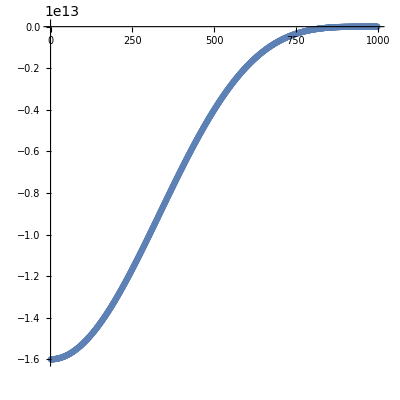

```mathematica
Clear[w,ww,d4w,q,h,g,nx,dx,tmax,deq,sistem,vars,r,rSparse,A,b,eq,wlist]

(* ŠE UCINKOVITEJSA METODA z diagonalizacijo *)
nx=1000;
dx=1/nx;
tmax=2;

(* deljene diference *)
d4w[t_,k_/;1≤k≤nx-1]:=(ww[k-2][t]-4 ww[k-1][t]+6 ww[k][t]-4 ww[k+1][t]+ww[k+2][t])/dx^4
d4w[t_,k_/;0==k]:=0 (*(ww[k+0][t]-4 ww[k+1][t]+6 ww[k+2][t]-4 ww[k+3][t]+ww[k+4][t,k+4])/dx^4*)
d4w[t_,k_/;nx==k]:=0 (*(ww[k-0][t]-4 ww[k-1][t]+6 ww[k-2][t]-4 ww[k-3][t]+ww[k-4][t,k-4])/dx^4*)

(* zacetni pogoji *)
q[x_]:=1 (*Piecewise[{{5,x<0.2},{0,True}}]*)
g[x_]:=0
h[x_]:=2 x (x-1/2) (x-1)

(* prosti robni pogoji *)
ww[0][t_]:=0;
ww[nx][t_]:=0;
ww[-1][t_]:=-ww[1][t];

ww[nx+1][t_]:=-ww[nx-1][t];

(* spremenljivke *)
vars=Table[ww[i][t],{i,1,nx-1}];

rhs=Table[q[i dx]-d4w[t,i]==0.,{i,1,nx-1}];(*desna stran enačbe w''=Aw+b*)
{b,A}=CoefficientArrays[rhs,vars];

Timing[{L,Q}=Eigensystem[A];]
(* oglejmo si lastne vrednosti in lastne vektorje *)
ListPlot[L,AspectRatio->1]
Manipulate[ListPlot[Q[[i]]],{i,1,nx-1,1}]
```

```mathematica
(* resimo diagonalno enačbo v splošnem *)
rSplosna=DSolveValue[{v''[t]==l v[t]+qb,v[0]==qg,v'[0]==qh},v,t];

(* začetni pogoji kot vektorji *)
iPos=Table[g[i dx],{i,1,nx-1}];
iVel=Table[h[i dx],{i,1,nx-1}];

(* napisemo resitev v diagonalni obliki *)
Timing[rDiag=rSplosna/.{l->L,qb->(Q.b),qg->(Q.iPos),qh->(Q.iVel)};]

(* naredimo 100 grafov ob različnih časih in jih transformiramo nazaj *)
moviesol=Table[-Transpose[Q].(Re[rDiag[t]]),{t,0,tmax,tmax/100}];
movieplt1=Table[ListLinePlot[Join[{ww[0][t]},sol,{ww[nx][t]}],PlotRange->{-0.05,0.05}],{sol,moviesol}];
ListAnimate[movieplt1, AnimationRate->.25]

(* Primerjava rešitev *)
sampleDiagY=-Transpose[Q].(Re[rDiag[1]]);
sampleDiag = Table[{i dx, sampleDiagY[[i]]}, {i,1,nx-1}];
Show[{ListLinePlot[sampleSimple],ListLinePlot[sampleSparse,ColorFunction->(Red&)],ListLinePlot[sampleDiag,ColorFunction->(Orange&)]}]

(* Je nekaj napake *)
Plot[Interpolation[sampleSimple][t]-Interpolation[sampleDiag][t],{t,0,tmax/2}]
```

## Zanemarjanje majhnih lastnih vrednosti

V zapuk pri rešitvi vzamemo le prvih nekaj lastnih vrednosti in lastnih vektorjev.

```mathematica
Clear[w,ww,d4w,q,h,g,nx,dx,tmax,deq,sistem,vars,r,rSparse,A,b,eq,wlist]

(* Zanemarjanje lastnih vrednosti *)
nx=100; (* itak je precej vseeno kakšen n ... *)
dx=1/nx;
tmax=2;

(* deljene diference *)
d4w[t_,k_/;1≤k≤nx-1]:=(ww[k-2][t]-4 ww[k-1][t]+6 ww[k][t]-4 ww[k+1][t]+ww[k+2][t])/dx^4
d4w[t_,k_/;0==k]:=0 (*(ww[k+0][t]-4 ww[k+1][t]+6 ww[k+2][t]-4 ww[k+3][t]+ww[k+4][t,k+4])/dx^4*)
d4w[t_,k_/;nx==k]:=0 (*(ww[k-0][t]-4 ww[k-1][t]+6 ww[k-2][t]-4 ww[k-3][t]+ww[k-4][t,k-4])/dx^4*)

(* zacetni pogoji *)
q[x_]:=1 (*Piecewise[{{5,x<0.2},{0,True}}]*)
g[x_]:=0
h[x_]:=2 x (x-1/2) (x-1)

(* prosti robni pogoji *)
ww[0][t_]:=0;
ww[nx][t_]:=0;
ww[-1][t_]:=-ww[1][t];

ww[nx+1][t_]:=-ww[nx-1][t];

(* spremenljivke *)
vars=Table[ww[i][t],{i,1,nx-1}];

rhs=Table[q[i dx]-d4w[t,i]==0.,{i,1,nx-1}];(*desna stran enačbe w''=Aw+b*)
{b,A}=CoefficientArrays[rhs,vars];

limit = 50; (* vzamemo največjih 50 *)

(* izračunamo lastne vektorje *)
Timing[{L,Q}=Eigensystem[A, -limit];]

(* splošna resitev *)
rSplosna=DSolveValue[{v''[t]==l v[t]+qb,v[0]==qg,v'[0]==qh},v,t];

(* začetni pogoji kot vektorji *)
iPos=Table[g[i dx],{i,1,nx-1}];
iVel=Table[h[i dx],{i,1,nx-1}];

(* napisemo resitev v diagonalni obliki *)
Timing[rDiag=rSplosna/.{l->L,qb->(Q.b),qg->(Q.iPos),qh->(Q.iVel)};]

(* naredimo 100 grafov ob različnih časih in jih transformiramo nazaj *)
moviesol=Table[-Transpose[Q].(Re[rDiag[t]]),{t,0,tmax,tmax/100}];
movieplt1=Table[ListLinePlot[Join[{ww[0][t]},sol,{ww[nx][t]}],PlotRange->{-0.05,0.05}],{sol,moviesol}];
ListAnimate[movieplt1, AnimationRate->.25]

(* Primerjava rešitev *)
sampleDiagCroppedY=-Transpose[Q].(Re[rDiag[1]]);
sampleDiagCropped = Table[{i dx, sampleDiagCroppedY[[i]]}, {i,1,nx-1}];
Show[{ListLinePlot[sampleDiag,ColorFunction->(Orange&)],ListLinePlot[sampleDiagCropped,ColorFunction->(Purple&)]}]

(* Pričakovana zelo majhna napaka *)
Plot[Interpolation[sampleDiagCropped][t]-Interpolation[sampleDiag][t],{t,0,tmax/2}]
```

### Aproksimacija višjega reda

Poskusimo še aproksimacjio s shemo četrtega reda. Tudi na robu aproksimiramo z enostanskimi diferencami.

```mathematica
Clear[w,ww,d4w,q,h,g,nx,dx,tmax,deq,sistem,vars,r,rSparse,A,b,eq,wlist]

(* DIREKTNA METODA z večjo natančnostjo *)
nx=50;(*stevilo tock diskretizacije*)
dx=1/nx;
tmax=2;(*do katerega casa naj izracuna resitev*)(*deljene diference*)

(* deljene diference cetrtega reda *)
d4w[t_,k_/;1≤k≤nx-1]:=(-1/6 ww[k-3][t]+2ww[k-2][t]-13/2 ww[k-1][t]+28/3 ww[k][t]-13/2 ww[k+1][t]+2ww[k+2][t]-1/6 ww[k+3][t])/dx^4
d4w[t_,k_/;0==k]:=(28/3ww[k][t]−111/2ww[k+1][t]+142ww[k+2][t]−1219/6ww[k+3][t]+176ww[k+4][t]−185/2ww[k+5][t]+82/3ww[k+6][t]−7/2ww[k+7][t])/dx^4
d4w[t_,k_/;nx==k]:=-(28/3ww[k][t]−111/2ww[k-1][t]+142ww[k-2][t]−1219/6ww[k-3][t]+176ww[k-4][t]−185/2ww[k-5][t]+82/3ww[k-6][t]−7/2ww[k-7][t])/dx^4

(* zacetni pogoji *)
q[x_]:=1 (*Piecewise[{{5,x<0.2},{0,True}}]*)
g[x_]:=0
h[x_]:=2 x (x-1/2) (x-1) (* malo ga sunemo na levi gor in na desni dol,da je bolj zanimivo *)

(* prosti robni pogoji *)
ww[0][t_]:=0;
ww[nx][t_]:=0;
ww[nx+1][t_]:=-ww[nx-1][t];
ww[nx+2][t_]:=-ww[nx-2][t];
ww[-1][t_]:=-ww[1][t];
ww[-2][t_]:=-ww[2][t];
```

```mathematica
(* generiranje sistema NDE po MOL*)
deq=d4w[t,x]+D[ww[x][t],{t,2}]==q[x dx];(* diskretizirana enačba v smeri x *)
sistem=Table[deq/.{x->i},{i,1,nx-1}];(* po vsaki točki diskretizacije *)
Print["Dolžina sistema: ",Length[sistem]]

(*generiranje zacetnih pogojev *)
pogoji={
Table[ww[k][0]==g[k dx],{k,1,nx-1}],
Table[ww[k]'[0]==h[k dx],{k,1,nx-1}]
};

(* spremenljivke *)
vars=Table[ww[i],{i,1,nx-1}];

(* resimo sistem*)
r=NDSolveValue[{sistem,pogoji},vars,{t,0,tmax}];

(* dodamo robne rešitve za prikaz *)
rSimpleHigh=Join[{ww[0]},r,{ww[nx]}];

Print["Število rešitev: ",Length[rSimpleHigh]]
```

Dolžina sistema: 49

Število rešitev: 51

```mathematica
(* upodobimo resitve *)
func=Table[-f[t],{f,rSimpleHigh}];
Plot[{func[[2]],func[[nx/2-5]]},{t,0,tmax}] (* točka na robu,točka na sredi *)

(* nosilec v odvisnosti od časa kot ploskev v ravnini (x,t) *)
parfunc=Table[{(i-1) dx,t,-10 rSimpleHigh[[i]][t]},{i,1,nx+1}];
ParametricPlot3D[parfunc,{t,0,tmax},PlotRange->All,AxesLabel->{"t","x","u"}] (*PlotRange->{{0,1},{0,5},{0,0.05}}]*)

(* nosilec v dejanski odvisnosti od časa *)
Animate[ListLinePlot[Table[{(i-1) dx,-rSimpleHigh[[i]][cas]},{i,1,nx+1}],PlotRange->{-0.05,0.05}],{cas,0,tmax},AnimationRate->.25]

(* shranimo si graf ob času 1 za naprej *)
sampleSimpleHigh=Table[{(i-1) dx,-rSimpleHigh[[i]][1]},{i,1,nx+1}];
Show[ListLinePlot[sampleSimple,PlotRange->{-0.05,0.05}],ListLinePlot[sampleSimpleHigh,ColorFunction->(Green &)]]

(* primerjamo z enako rešitvijo, ki pa je imela aproksimacijo drugega reda *)
ListLinePlot[Map[Last,sampleSimple]-Map[Last,sampleSimpleHigh]]
```

## Primerjava z analitično rešitvijo

Zmislimo si funkcijo, ki ustreza robnim pogojem, jo vstavimo v enačbo, dobimo desno stran in začetne pogoje. 
Nato rešimo enačbo s temi pogoji in preverimo, ali nazaj dobimo funkcijo, ki smo si jo izmislili. (Ta trik mi je zelo všeč!)

Desna stran q je odvisna tudi od t, ampak to naših metod ne ovira.

```mathematica
(* izračuanmo polinom cetrte stopnje, ki ustreza robnim pogojem *)
Clear[p,r,rr,r,g,h,q]
p[x_] := a x^4 + b x^3 + c x^2 + d x + e
r = First[Solve[p''[0] == 0 && p''[1] == 0 && p[0] == 0 && p[1] == 0 && p[1/2] == 1/100, {a, b, c, d, e}]];
rr[x_] := Evaluate[p[x] /. r]

(* naša rešitev -- mora biti produkt, ker lahko resujemo s separacijo *)
u[x_, t_] := rr[x] Sin[t]
Plot3D[u[x, t], {x, 0, 1}, {t, 0, 8}]
g[x_] := u[x, 0]
h[x_] :=Derivative[0,1][u][x, 0]
q[x_, t_] := Evaluate[Simplify[D[u[x, t], {x, 4}] + D[u[x, t], {t, 2}]]]

(* Primerjali bomo ob času tCmp *)
tCmp = 1.8
```

-Graphics3D-

1.8

```mathematica
(* deljene diference *)
d4w[t_,k_/;1≤k≤nx-1]:=(ww[k-2][t]-4 ww[k-1][t]+6 ww[k][t]-4 ww[k+1][t]+ww[k+2][t])/dx^4
d4w[t_,k_/;0==k]:=0 (*(ww[k+0][t]-4 ww[k+1][t]+6 ww[k+2][t]-4 ww[k+3][t]+ww[k+4][t,k+4])/dx^4*)
d4w[t_,k_/;nx==k]:=0 (*(ww[k-0][t]-4 ww[k-1][t]+6 ww[k-2][t]-4 ww[k-3][t]+ww[k-4][t,k-4])/dx^4*)
```

#### Običajna metoda delne integracije

```mathematica
Clear[ww,w,nx,dx,tmax,deq,sistem,vars,r,rSimple,func,parfunc,pltSimple]
(* DIREKTNA METODA,do nx=30,z nekaj potrpljenja *)
nx=30;(* stevilo tock diskretizacije *)
dx=1/nx;
tmax=4;(* do katerega casa naj izracuna resitev *)

(* prosti robni pogoji *)
ww[0][t_]:=0;
ww[nx][t_]:=0;
ww[-1][t_]:=-ww[1][t];
ww[nx+1][t_]:=-ww[nx-1][t];
```

```mathematica
(*generiranje sistema NDE po MOL*)
deq=d4w[t,x]+D[ww[x][t],{t,2}]==q[x dx,t];(* diskretizirana enačba v smeri x *)
sistem=Table[deq/.{x->i},{i,1,nx-1}];(* po vsaki točki diskretizacije *)
pogoji={Table[ww[k][0]==g[k dx],{k,1,nx-1}],Table[ww[k]'[0]==h[k dx],{k,1,nx-1}]};
vars=Table[ww[i],{i,1,nx-1}];
r=NDSolveValue[{sistem,pogoji},vars,{t,0,tmax}];
rSimple=Join[{ww[0]},r,{ww[nx]}];
data = Table[{(i-1) dx,-rSimple[[i]][tCmp]},{i,1,nx+1}];
rSimpleF = Interpolation[data];
```

```mathematica
(* rešitvi sta popolnoma pokriti *)
Manipulate[Plot[{Interpolation[Table[{(i-1) dx,-rSimple[[i]][tt]},{i,1,nx+1}]][x],-u[x,tt]},{x,0,1},PlotRange->{-0.03,0.03}],{tt,0,4}]
(* napaka *)
Manipulate[Plot[{Interpolation[Table[{(i-1) dx,-rSimple[[i]][tt]},{i,1,nx+1}]][x]+u[x,tt]},{x,0,1},PlotRange->{-0.00002,0.00002}],{tt,0,4}]
```

#### Diagonalizacija na roke

```mathematica
Clear[w,nx,dx,tmax,deq,sistem,vars,r,rSparse,A,b,eq,wlist]

nx=10;
dx=1/nx;
tmax=2;

(* prosti robni pogoji *)
ww[0][t_]:=0;
ww[nx][t_]:=0;
ww[-1][t_]:=-ww[1][t];
ww[nx+1][t_]:=-ww[nx-1][t];
```

```mathematica
vars=Table[ww[i][t],{i,1,nx-1}];
rhs=Table[q[i dx,t]-d4w[t,i]==0.,{i,1,nx-1}];(* desna stran enačbe w''=Aw+b *)
{b,A}=CoefficientArrays[rhs,vars];
{L,Q}=Eigensystem[A];
qb=Q.b//Simplify;
qb1 = Table[qbb[[1]],{qbb,qb}];

rSplosna=DSolveValue[{v''[t]==l v[t]+Sin[t]qbb1,v[0]==qg,v'[0]==qh},v,t];

(* začetni pogoji kot vektorji *)
iPos=Table[g[i dx],{i,1,nx-1}];
iVel=Table[h[i dx],{i,1,nx-1}];

(* napisemo resitev v diagonalni obliki *)
rDiag=rSplosna/.{l->L,qbb1->qb1,qg->(Q.iPos),qh->(Q.iVel)};
data=Re[-Transpose[Q].(rDiag[tCmp])];
data=Join[{0},data,{0}];
data = Table[{(i-1)dx,data[[i]]},{i,1,Length[data]}];
rDiagF = Interpolation[data]
```

InterpolatingFunction[{{0., 1.}}, <>]

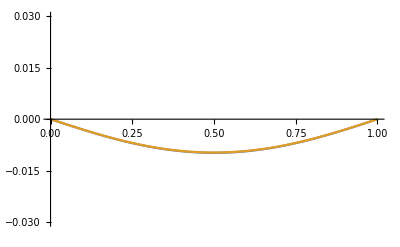

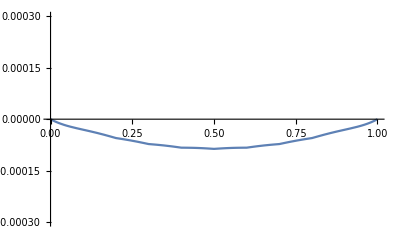

```mathematica
(* primerjava, funckiji sta zopet pokriti,  *)
Plot[{rDiagF[x],-u[x,tCmp]},{x,0,1},PlotRange->{-0.03,0.03}]
(* napaka *)
Plot[{rDiagF[x]+u[x,tCmp]},{x,0,1},PlotRange->{-0.0003,0.0003}]
```